```mathematica
a1 = 0;a2=3;b1=0;b2=2;
```

```mathematica
f[x_,y_]:=-x^2;
AB[x_,y_]:=(3-x)*x+0.2;
BC[x_,y_]:=1/5;
CD[x_,y_]:=1/5;
DA[x_,y_]:=y*(2-y)+0.2;
```

```mathematica
n = 20;m=20;eps=0.001;
```

```mathematica
zy=(b2-b1)/(m-1);
```

```mathematica
zx=(a2-a1)/(n-1);
```

```mathematica
Array[F,{n,m},{0,0}];
```

```mathematica
Array[U,{n,m},{0,0}];
```

```mathematica
Do[F[i,j]=N[f[i*zx, j*zy]];U[i,j]=0,{i,0,n-1},{j,0,m-1}];
```

```mathematica
Do[U[i,m-1]=AB[i*zx,(m-1)*zy];
U[i,0]=CD[i*zx, 0],{i,0,n-1}];

Do[U[n-1,j]=BC[(n-1)*zx,j*zy];U[0,j]=DA[0,j*zy], {j,0,m-1}];
```

```mathematica
e=10;
```

```mathematica
k=0;
```

```mathematica
While[e>eps, ++k;e=0;
Do[v=1/8((2+0.1j *zy^2)*U[i-1,j]+(2-0.1*j*zy^2)U[i+1,j]+2U[i,j-1]+2U[i,j+1]-2zx*zy*F[i,j]);e=Max[Abs[v-U[i,j]],e];U[i,j]=v, {i,1,n-2},{j,1,m-2}]];
```

```mathematica
Print["k = ",k , " zx = ", N[zx], " zy = ", N[zy]];
```

k = 160 zx = 0.157895 zy = 0.105263

```mathematica
ListPlot3D[Array[U,{n,m}, {0,0}], DataRange->{{b1,b2}, {a1,a2}}]
```

-Graphics3D-

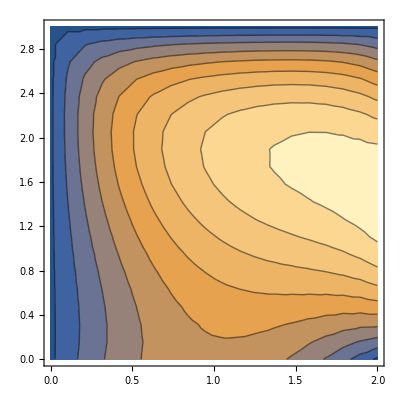

```mathematica
ListContourPlot[Array[U,{n,m}, {0,0}], DataRange->{{b1,b2}, {a1,a2}}]
```

```mathematica
(36.1+35.65+37.8+35.45)/4
```

36.25

```mathematica
(3610+3565+3780+3545)/4
```

3625

```mathematica
(120.5+190.5)/(2+3)
```

62.2

```mathematica
(120.5/2+190.5/3)/2
```

61.875

```mathematica
123.75/2
```

61.875

```mathematica
295/6
```

295/6

```mathematica
N[(9/2+13/3)/2]
```

4.41667

```mathematica
N[(9+13)/(2+3)]
```

4.4